```mathematica
produceDTPlot[distAndTime_,distMax_,binWidth_]:= Module[{tableOfDistances,binnedDistances,tableOfDistancesIndices,tableOfTimes,timeAverages,timeBins,averagesWithBins},
tableOfDistances = Table[distAndTime[[i,1]],{i,Length[distAndTime]}];
binnedDistances=BinLists[tableOfDistances,{0,distMax,binWidth}];
tableOfDistancesIndices = Table[Flatten[Table[Position[tableOfDistances,binnedDistances[[j,i]],3],{i,Length[binnedDistances[[j]]]}]],{j,Length[binnedDistances]}];
tableOfTimes = Table[Table[distAndTime[[tableOfDistancesIndices[[j,i]],2]],{i,Length[tableOfDistancesIndices[[j]]]}],{j,Length[tableOfDistancesIndices]}];
timeAverages = Table[Mean[tableOfTimes[[i]]],{i,Length[tableOfTimes]-1}];
timeBins = Table[.25+(i-1)/2,{i,Length[timeAverages]}];
averagesWithBins = Table[{timeBins[[i]],timeAverages[[i]]},{i,Length[timeAverages]}]
]
torDistancesAndTimes=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torus_distance_and_time.csv"];
spDistancesAndTimes = Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/sp_distance_and_time.csv"];
torBinnedAverages = produceDTPlot[torDistancesAndTimes,10,.5]
spBinnedAverages = produceDTPlot[spDistancesAndTimes,10,.5]
```

{{0.25,254/5},{0.75,251/5},{1.25,962/19},{1.75,2281/45},{2.25,3259/63},{2.75,3023/59},{3.25,4001/78},{3.75,3954/77},{4.25,2915/57},{4.75,3539/69},{5.25,4018/79},{5.75,1574/31},{6.25,4893/95},{6.75,3536/69},{7.25,1947/37},{7.75,2695/51},{8.25,1630/31},{8.75,1034/19},{9.25,331/6}}

{{0.25,371/8},{0.75,213/5},{1.25,427/10},{1.75,1696/41},{2.25,1067/27},{2.75,2111/54},{3.25,2347/60},{3.75,2939/77},{4.25,1364/35},{4.75,2605/64},{5.25,883/22},{5.75,2677/66},{6.25,2535/61},{6.75,735/17},{7.25,305/7},{7.75,2189/49},{8.25,2774/59},{8.75,1469/31},{9.25,1806/37}}

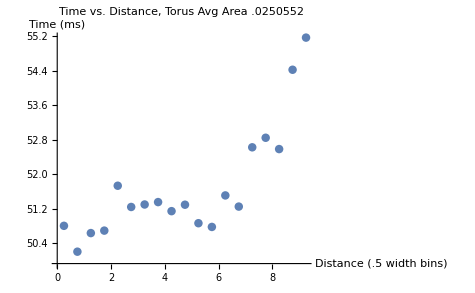

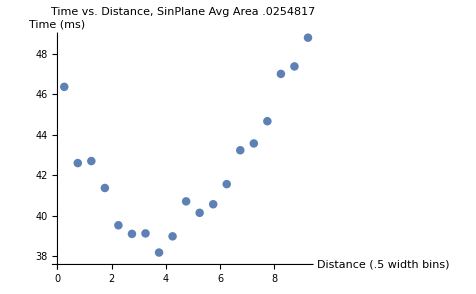

```mathematica
torTTCDataPlot = ListPlot[torBinnedAverages,PlotLabel->"Time vs. Distance, Torus Avg Area .0250552", AxesLabel->{"Distance (.5 width bins)","Time (ms)"}]
spTTCDataPlot = ListPlot[spBinnedAverages,PlotLabel->"Time vs. Distance, SinPlane Avg Area .0254817", AxesLabel->{"Distance (.5 width bins)","Time (ms)"}]
```

```mathematica
fitModel= LinearModelFit[averagesWithBins,{1,x},x];
nonLinearFitModel = NonlinearModelFit[averagesWithBins,x^a+b,{a,b},x];
r2line = fitModel["RSquared"]
r2power=nonLinearFitModel["RSquared"]
{fitModel,r2line,nonLinearFitModel,r2power}
forceFit = Plot[{fitModel[x],nonLinearFitModel[x]},{x,0,10}];
```

0.616885

0.999721